# OPERM5RandomnessTest

Test a sequence of 0s and 1s for randomness using an overlapping permutations test where permutations are of length 5.

## DefinitionDefinitionDefine your function using the name you gave in the Title line above. You can add input cells and extra code to define additional input cases or prerequisites. All definitions, including dependencies, will be included in the generated resource function. This section should be evaluated before creating the Examples section below.

```mathematica
$cts=Values@KeySort@(CountsBy[Tuples[{0,1},5],Total]/(N@Length[Tuples[{0,1},5]]));
operm5stat=Total[(PadRight[Values@KeySort@(Counts[Total/@Subsequences[#,{5}]]/(Length[#]-4)),6]-$cts)^2/$cts]&;
```

{0.03125,0.15625,0.3125,0.3125,0.15625,0.03125}

```mathematica
$βoperm5[seqleng_]:=5.154091641671948/seqleng^0.9799168145415045;(*Need to recalculate with more points and a larger sample size*);
$αoperm5=2.0568433064986755;(*Need to recalculate with more points and a larger sample size*)operm5dist[seqleng_]:=GammaDistribution[$αoperm5,$βoperm5[seqleng]];
```

```mathematica
operm5Test[seq_]:=<|"TestStatistic"->operm5stat[seq],"PValue"->1-CDF[operm5dist[Length[seq]],operm5stat[seq]]|>
```

```mathematica
OPERM5RandomnessTest::seqlength="List length is less than 250!";
```

```mathematica
OPERM5RandomnessTest[seq_List/;Length[seq]<250]:=Message[OPERM5RandomnessTest::seqlength];
OPERM5RandomnessTest[seq_List/;VectorQ[seq,#==0||#==1&]]:=1-CDF[operm5dist[Length[seq]],operm5stat[seq]];
OPERM5RandomnessTest[seq_List/;VectorQ[seq,#==0||#==1&],"PValue"]:=1-CDF[operm5dist[Length[seq]],operm5stat[seq]];
OPERM5RandomnessTest[seq_List/;VectorQ[seq,#==0||#==1&],"TestStatistic"]:=operm5stat[seq];
```

## Documentation

### UsageUsageDocument input usage cases by first typing an input structure, then pressing to add a brief explanation of the function’s behavior for that structure. Pressing repeatedly will create new cases as needed. Every input usage case defined above should be demonstrated explicitly here. See existing documentation pages for examples.

OPERM5RandomnessTest[sequence]

returns a p-value associated with a test for randomness of sequence.

OPERM5RandomnessTest[sequence,"property"]

returns a property associated with a test for randomness of sequence.

### Details & OptionsDetails & OptionsGive a detailed explanation of how the function is used and configured (e.g. acceptable input types, result formats, options specifications, background information). This section may include multiple cells, bullet lists, tables, hyperlinks and additional styles/structures as needed. Add any other information that may be relevant, such as when the function was first discovered or how and why it is used within a given field. Include all relevant background or contextual information related to the function, its development, and its usage.

Properties include

"TestStatistic" | Returns the test statistic
"PValue" | Returns the p-value associated with the test

The test statistic is generated by creating a chi square-like statistic that measures the difference between a certain number of permutations present over all subsequences and the expected number of permutations present over all subsequences.

The test only works for sequences of 0s and 1s

OPERM5RandomnessTest results are valid only for sequence lengths greater than 250.

## ExamplesExamplesDemonstrate the function’s usage, starting with the most basic use case and describing each example in a preceding text cell. Within a group, individual examples can be delimited by inserting page breaks between them (either using "[Right-click]"" ▶ ""Insert Page Break" between cells or through the menu using "Insert"" ▶ ""Page Break"). Examples should be grouped into Subsection and Subsubsection cells similarly to existing documentation pages. Here are some typical Subsection names and the types of examples they normally contain: "◼ ""Basic Examples: "most basic function usage "◼ ""Scope: "input and display conventions, standard computational attributes (e.g. threading over lists) "◼ ""Options: "available options and parameters for the function "◼ ""Applications: "standard industry or academic applications "◼ ""Properties and Relations: "how the function relates to other functions "◼ ""Possible Issues: "limitations or unexpected behavior a user might experience "◼ ""Neat Examples: "particularly interesting, unconventional, or otherwise unique usage

### Basic Examples

Generate a sequence of random integers and apply an overlapping permutations-based test:

```mathematica
sequence=RandomInteger[{0,1},1000];
```

Visualize the sequence:

```mathematica
ArrayPlot[Partition[sequence,16]ᵀ,ImageSize->Large]
```

-Graphics-

```mathematica
OPERM5RandomnessTest[sequence,"TestStatistic"]
```

0.00801923

```mathematica
OPERM5RandomnessTest[sequence,"PValue"]
```

0.625104

### Scope

### Options

### Applications

Test the randomness of rule 30:

```mathematica
rule30seq=CellularAutomaton[30, {{1}, 0}, {10000,0}]ᵀ⟦1⟧;
```

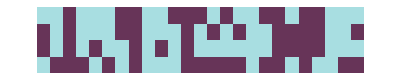

```mathematica
ArrayPlot[Partition[Take[rule30seq,100],25],]
```

```mathematica
OPERM5RandomnessTest[rule30seq]
```

0.764772

Reject the randomness of a non-random sequence:

```mathematica
subsequence=RandomInteger[{0,1},100];
```

```mathematica
sequence=Flatten[Table[subsequence,20]];
```

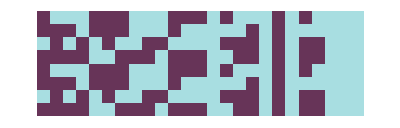

```mathematica
ArrayPlot[Partition[Take[sequence,200],25],]
```

```mathematica
OPERM5RandomnessTest[sequence]
```

0.

### Properties and Relations

### Possible Issues

### Neat Examples

Visualize the sampling distribution of the test statistic:

```mathematica
samp=OPERM5RandomnessTest[#,"TestStatistic"]&/@RandomInteger[{0,1},{1000,1000}];
```

```mathematica
Histogram[samp,Automatic,"PDF"]
```

-Graphics-

```mathematica
dist=FindDistribution[samp,TargetFunctions->{GammaDistribution}]
```

GammaDistribution[2.08679,0.00592864]

```mathematica
Show[Histogram[samp,Automatic,"PDF"],Plot[PDF[dist,x],{x,0,.1}]]
```

-Graphics-

## Source & Additional Information

### Contributed ByContributed ByEnter the name of the person, people or organization that should be publicly credited with contributing this function.

Emmy/Noah Blumenthal
noahb320@gmail.com
emmyb320@bu.edu

### KeywordsKeywordsList relevant terms (e.g. functional areas, algorithm names, related concepts) that should be used to include the function in search results.

Randomness

Statistics

### Categories

Cloud & Deployment |  Core Language & Structure
 Data Manipulation & Analysis |  Engineering Data & Computation
 External Interfaces & Connections |  Financial Data & Computation
 Geographic Data & Computation |  Geometry
 Graphs & Networks |  Higher Mathematical Computation
 Images |  Just For Fun
 Knowledge Representation & Natural Language |  Machine Learning
 Notebook Documents & Presentation |  Programming Utilities
 Repository Tools |  Scientific and Medical Data & Computation
 Social, Cultural & Linguistic Data |  Sound
 Strings & Text |  Symbolic & Numeric Computation
 System Operation & Setup |  Time-Related Computation
 User Interface Construction |  Visualization & Graphics

### Related SymbolsRelated SymbolsList up to twenty documented, system-level Wolfram Language symbols related to the function.

### Related Resource ObjectsRelated Resource ObjectsList the names of published resource objects from any Wolfram repository that are related to this function.

ChiSquareRandomnessTest

### Source/Reference CitationSource/Reference CitationGive a bibliographic-style citation for the original source of the function and/or its components (e.g. a published paper, algorithm, or code repository).

Source, reference or citation information

### LinksLinksList additional URLs or hyperlinks for external information related to the function.

### TestsTestsSpecify an optional list of tests for verifying that the function is working properly in any environment. Tests can be specified as Input/Output cell pairs or as symbolic VerificationTest expressions for including additional options.

## Author Notes

This overlapping permutations test requires a sequence of length at least 250. The test is more accurate when the sequence length is at least 1000.

## Submission NotesSubmission NotesEnter any additional information that you would like to communicate to the reviewer here. This section will not be included in the published resource.

Additional information for the reviewer.